# Distance Measures

Peter Burbery

I exam different ways to measure distances between points on Earth

## Learning how latitude and longitude and degrees work

Find my current position:

```mathematica
Here
```

GeoPosition[{38.41,-82.44}]

Generate a DMS String:

```mathematica
DMSString[Here]
```

38°24'36.000"N 82°26'24.000"W

Generate a list with degrees, minutes and seconds:

```mathematica
DMSList[Here]
```

{{38,24,36.},{-82,-26,-24.}}

Convert a DMS String from the output of DMSString and DMSList:

```mathematica
FromDMS["38°24'36.000\"N 82°26'24.000\"W"]
```

{38.41,-82.44}

Convert a mixed unit angle for my latitude to a decimal angle:

```mathematica
FromDMS[{38,24,36.0000000000133}]
```

38.41

longitude angle:

```mathematica
FromDMS[{-82,-26,-23.999999999991815}]
```

-82.44

Compute my latitude:

```mathematica
Latitude[Here]
```

38.41 °

Longitude:

```mathematica
Longitude[Here]
```

-82.44 °

Latitude and longitude:

```mathematica
LatitudeLongitude[Here]
```

{38.41 °,-82.44 °}

Manually enter a position:

```mathematica
Degree{Quantity[38.410000000000004, "AngularDegrees"],Quantity[-82.44, "AngularDegrees"]}
```

{0.670381 °,-1.43885 °}

```mathematica
{38,33}Degree
```

{38 °,33 °}

```mathematica
GeoPosition[{38,33}Degree]
```

GeoPosition[{38 °,33 °}]

## Learning coordinate systems:

Express the position of a place:

Find my location:

```mathematica
GeoPosition[Here]
```

GeoPosition[{38.41,-82.44}]

Find the Empire State building's location:

```mathematica
GeoPosition[ResourceFunction["WikidataGeoPosition"]["Empire State Building"]]
```

GeoPosition[{40.7483,-73.9853}]

Find the position with Cartesian coordinates:

```mathematica
GeoPositionXYZ[Here]
```

GeoPositionXYZ[{658385.,-4.96078×10^6,3.94121×10^6}]

```mathematica
GeoPositionXYZ[ResourceFunction["WikidataGeoPosition"]["Empire State Building"]]
```

GeoPositionXYZ[{1.33497×10^6,-4.65109×10^6,4.14129×10^6}]

Find the position east, north, and up relative to the center of the Earth:

```mathematica
GeoPositionENU[Here,GeoPositionXYZ[{0,0,0}]]
```

GeoPositionENU[{-4.96078×10^6,-658385.,3.94121×10^6},GeoPosition[{90.,0.,-6.35675×10^6}]]

If I rearrange the first part this is equal to the output from GeoPositionXYZ:

remove the head GeoPositionENU

```mathematica
First[GeoPositionENU[Here,GeoPositionXYZ[{0,0,0}]]]
```

{-4.96078×10^6,-658385.,3.94121×10^6}

take the east and north components:

```mathematica
Take[First[GeoPositionENU[Here,GeoPositionXYZ[{0,0,0}]]],2]
```

{-4.96078×10^6,-658385.}

reverse the components to obtain x and y:

```mathematica
Reverse[Take[First[GeoPositionENU[Here,GeoPositionXYZ[{0,0,0}]]],2]]
```

{-658385.,-4.96078×10^6}

change to the XYZ sign convention by multiplying the first element by -1:

```mathematica
{-1,1}*Reverse[Take[First[GeoPositionENU[Here,GeoPositionXYZ[{0,0,0}]]],2]]
```

{658385.,-4.96078×10^6}

Join the result with the up component:

```mathematica
Join[{-1,1}*Reverse[Take[First[GeoPositionENU[Here,GeoPositionXYZ[{0,0,0}]]],2]],Drop[First[GeoPositionENU[Here,GeoPositionXYZ[{0,0,0}]]],2]]
```

{658385.,-4.96078×10^6,3.94121×10^6}

Compute the xyz position value for my location:

```mathematica
GeoPositionXYZ[Here]
```

GeoPositionXYZ[{658385.,-4.96078×10^6,3.94121×10^6}]

Check that they are the same:

```mathematica
Join[{-1,1}*Reverse[Take[First[GeoPositionENU[Here,GeoPositionXYZ[{0,0,0}]]],2]],Drop[First[GeoPositionENU[Here,GeoPositionXYZ[{0,0,0}]]],2]]==First[GeoPositionXYZ[Here]]
```

True

## Projecting coordinates on a grid for display on a map:

When a map projection is created, the actual coordinates are shifted to new locations based on the geometry of the projection. I can compute the coordinates transformed values with regards to the projection with GeoGridPosition.

Transform coordinates to the Bonne projection:

```mathematica
GeoGridPosition[GeoPosition[{37.,-19.,0}],"Bonne"]
```

GeoGridPosition[{-0.262842,0.673854,0},Bonne]

```mathematica
GeoGridPosition[Here,"Bonne"]
```

GeoGridPosition[{-0.973572,1.15548},Bonne]

Change the center of the projection:

```mathematica
GeoGridPosition[GeoPosition[{37.,-19.,0}],{"Bonne","Centering"->{-35,-100}}]
```

GeoGridPosition[{0.980327,1.12387,0},{Bonne,Centering→{-35,-100}}]

```mathematica
GeoGridPosition[GeoPosition[{37.,-19.,0}],{"Bonne","Centering"->{-38,27}}]
```

GeoGridPosition[{-0.613176,0.807373,0},{Bonne,Centering→{-38,27}}]

Specify the standard parallels for a projection:

```mathematica
GeoGridPosition[GeoPosition[{37.,-19., 0}],{"Albers","Centering"->GeoPosition[{40,-100}],"StandardParallels"->{20,50}}]
```

GeoGridPosition[{0.982487,0.351557,0},{Albers,Centering→GeoPosition[{40,-100}],StandardParallels→{20,50}}]

Apply a transformation with the Albers projection:

```mathematica
p=GeoGridPosition[Here,"Albers"]
```

GeoGridPosition[{-0.915891,1.03469},Albers]

```mathematica
p["Properties"]
```

{AbsoluteTime,Count,Data,DateList,DateObject,Datum,Depth,Dimension,Elevation,GeoProjection,GridX,GridXY,GridY,PackingType}

Display the properties of my position in the Albers projection in a column:

```mathematica
AssociationMap[p,p["Properties"]]//Normal//Column
```

AbsoluteTime→3.8706242608440918×10^9
Count→1
Data→{-0.915891,1.03469}
DateList→{2022,8,27,21,24,20.8440918}
DateObject→Sat 27 Aug 2022 21:24:20GMT
Datum→ITRF00
Depth→0
Dimension→2
Elevation→0
GeoProjection→Albers
GridX→-0.915891
GridXY→{-0.915891,1.03469}
GridY→1.03469
PackingType→None

Manipulate the United States points:

```mathematica
pos=GeoPosition[CountryData["UnitedStates","Coordinates"]]
```

GeoPosition[…]

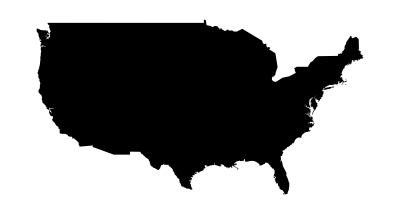

```mathematica
Graphics[Polygon[First[GeoGridPosition[pos,"Mercator"]]]]
```

Use the Cassini projection:

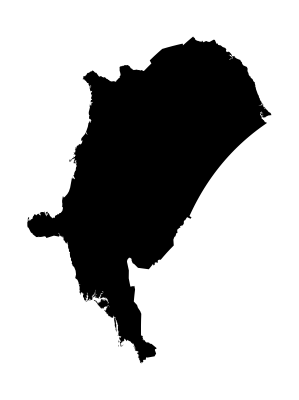

```mathematica
Graphics[Polygon[First[GeoGridPosition[pos,{"Cassini","Centering"->{27,18}}]]]]
```

Alternative method:

```mathematica
GeoGraphics[Polygon[GeoPosition[CountryData["UnitedStates","Coordinates"]]],GeoProjection->{"Cassini","Centering"->{27,18}}]
```

-Graphics-

```mathematica
GeoGraphics[Polygon[GeoPosition[CountryData["UnitedStates","Coordinates"]]],GeoProjection->{"Cassini","Centering"->{27,18}},ImageSize->1000,GeoBackground->{"Coastlines", "VectorLabels"}]
```

GeoServer::vtiles: Unable to download one or more vector tiles.

-Graphics-

```mathematica
GeoGraphics[Polygon[GeoPosition[CountryData["UnitedStates","Coordinates"]]],GeoProjection->{"Cassini","Centering"->{27,18}},ImageSize->1000,GeoBackground->{"VectorBusiness"}]
```

-Graphics-

Find my antipode:

```mathematica
GeoAntipode[Here]
```

GeoPosition[{-38.41,97.56}]